```mathematica
pulseRate:=27
CoeffN1:=Round[891/pulseRate]
CoeffN2:=Round[2412/pulseRate]
CoeffN3:=Round[3700/pulseRate]
```

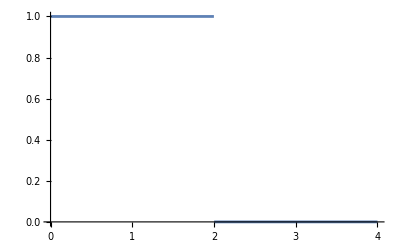

```mathematica
A:=Piecewise[{{1,0<t<2}, {1,0<t<2},{0,2<t<4}}]
Plot[A,{t,0,4}]
```

```mathematica
At:=FourierSeries[A,t,10]
Ac1:=Abs[FourierCoefficient[A,t,CoeffN1]]
N[Ac1]
Ac2:=Abs[FourierCoefficient[A,t,CoeffN2]]
N[Ac2]
Ac3:=Abs[FourierCoefficient[A,t,CoeffN3]]
N[Ac3]
```

0.0096449

0.00307605

0.00218987

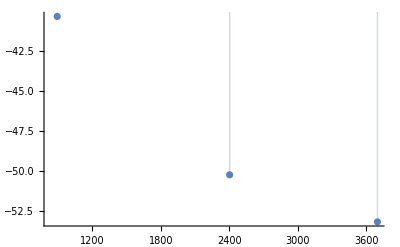

```mathematica
ListPlot[{{pulseRate*CoeffN1,20*Log10[Ac1]},{pulseRate*CoeffN2,20*Log10[Ac2]},{pulseRate*CoeffN3,20*Log10[Ac3]}},Filling->Axis]
```

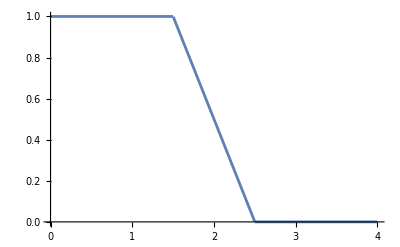

```mathematica
B:=Piecewise[{{1,0<t<1.5},{2.5-t,1.5<t<2.5},{0,2.5<t<4}}]
Plot[B,{t,0,4}]
```

```mathematica
Bt:=FourierSeries[B,t,10]
Bc1:=Abs[FourierCoefficient[B,t,CoeffN1]]
N[Bc1]
Bc2:=Abs[FourierCoefficient[B,t,CoeffN2]]
N[Bc2]
Bc3:=Abs[FourierCoefficient[B,t,CoeffN3]]
N[Bc3]
```

0.0046149

0.00179788

0.00115413

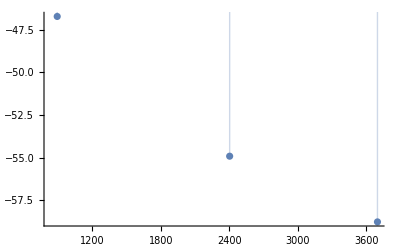

```mathematica
ListPlot[{{pulseRate*CoeffN1,20*Log10[Bc1]},{pulseRate*CoeffN2,20*Log10[Bc2]},{pulseRate*CoeffN3,20*Log10[Bc3]}},Filling->Axis]
```

```mathematica
20*Log10[N[Ac1/Ac2]]
20*Log10[N[Bc1/Bc2]]
20*Log10[N[Bc3/Bc3]]
20*Log10[N[Ac1/Bc1]]
20*Log10[N[Ac2/Bc2]]
20*Log10[N[Ac3/Bc3]]
```

9.92609

8.18805

0.

6.40271

4.66467

5.56325

```mathematica
N[20*Log10[2400/900]]
```

8.51937